```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
Pp[rt_,mt_,kt_]:=-4/3 rt-kt^2;
Qq[rt_,mt_,kt_]:=-mt^2/2+kt^3-4 kt rt;
xh[rt_,mt_,kt_]:=(-Qq[rt,mt,kt]+√(Qq[rt,mt,kt]^2+Pp[rt,mt,kt]^3))^(1/3);
z0[rt_,mt_,kt_]:=2 kt+xh[rt,mt,kt]-Pp[rt,mt,kt]/xh[rt,mt,kt];
e0[rt_,mt_,kt_]:=z0[rt,mt,kt]^(1/2);
app[rt_,mt_,kt_]:=1/2((+e0[rt,mt,kt])+√(-(+e0[rt,mt,kt])^2-2mt/(+e0[rt,mt,kt])+6 kt));
apm[rt_,mt_,kt_]:=1/2((-e0[rt,mt,kt])+√(-(-e0[rt,mt,kt])^2-2mt/(-e0[rt,mt,kt])+6 kt));
amp[rt_,mt_,kt_]:=1/2((+e0[rt,mt,kt])-√(-(+e0[rt,mt,kt])^2-2mt/(+e0[rt,mt,kt])+6 kt));
amm[rt_,mt_,kt_]:=1/2((-e0[rt,mt,kt])-√(-(-e0[rt,mt,kt])^2-2mt/(-e0[rt,mt,kt])+6 kt));
zerocheck[rt_,mt_,kt_]:=Simplify[app[rt,mt,kt]+apm[rt,mt,kt]+amp[rt,mt,kt]+amm[rt,mt,kt]]

a1[rt_,mt_,kt_]:=apm[rt,mt,kt];
a2[rt_,mt_,kt_]:=app[rt,mt,kt];
a3[rt_,mt_,kt_]:=amp[rt,mt,kt];
a4[rt_,mt_,kt_]:=amm[rt,mt,kt];
mm[rt_,mt_,kt_]:=((a2[rt,mt,kt]-a3[rt,mt,kt])(a1[rt,mt,kt]-a4[rt,mt,kt]))/((a1[rt,mt,kt]-a3[rt,mt,kt])(a2[rt,mt,kt]-a4[rt,mt,kt]));
rho[rt_,mt_,kt_,lam_]:=1/2 √(lam/3(a1[rt,mt,kt]-a3[rt,mt,kt])(a2[rt,mt,kt]-a4[rt,mt,kt]));
a[rt_,mt_,kt_,lam_,tau_]:=(a1[rt,mt,kt](a2[rt,mt,kt]-a4[rt,mt,kt])-a2[rt,mt,kt](a1[rt,mt,kt]-a4[rt,mt,kt])JacobiSN[rho[rt,mt,kt,lam] tau,mm[rt,kt,mt]]^2)/((a2[rt,mt,kt]-a4[rt,mt,kt])-(a1[rt,mt,kt]-a4[rt,mt,kt])JacobiSN[rho[rt,mt,kt,lam] tau,mm[rt,mt,kt]]^2)

(*t[rt_,mt_,kt_,lam_]:=NIntegrate[a[rt,mt,kt,lam,tau],{tau,7.5,7.5+2 EllipticK[mm[rt,mt,kt]]/rho[rt,mt,kt,lam]}]

Plot0=Plot3D[Im[t[10^((4/3)RT),10^MT,1,1]],{RT,-3/2,3},{MT,-3/2,3},PlotRange->{-2,3},WorkingPrecision->3,PlotPoints->10,MaxRecursion->0]*)


a1p[rt_,mt_,kt_]:=a2[rt,mt,kt];
a2p[rt_,mt_,kt_]:=a3[rt,mt,kt];
a3p[rt_,mt_,kt_]:=a1[rt,mt,kt];
a4p[rt_,mt_,kt_]:=a4[rt,mt,kt];

a12[rt_,mt_,kt_]:=a1p[rt,mt,kt]-a2p[rt,mt,kt];
a13[rt_,mt_,kt_]:=a1p[rt,mt,kt]-a3p[rt,mt,kt];
a14[rt_,mt_,kt_]:=a1p[rt,mt,kt]-a4p[rt,mt,kt];
a23[rt_,mt_,kt_]:=a2p[rt,mt,kt]-a3p[rt,mt,kt];
a24[rt_,mt_,kt_]:=a2p[rt,mt,kt]-a4p[rt,mt,kt];
a34[rt_,mt_,kt_]:=a3p[rt,mt,kt]-a4p[rt,mt,kt];
m0[rt_,mt_,kt_]:=(a12[rt,mt,kt] a34[rt,mt,kt])/(a13[rt,mt,kt] a24[rt,mt,kt]);
CK[rt_,mt_,kt_]:=a13[rt,mt,kt](a34[rt,mt,kt]^2-a12[rt,mt,kt]^2-4/3 a14[rt,mt,kt] a24[rt,mt,kt]);
CE[rt_,mt_,kt_]:=8 kt*(a13[rt,mt,kt] a24[rt,mt,kt])/a23[rt,mt,kt];
CPi[rt_,mt_,kt_]:=(a13[rt,mt,kt]^2-a24[rt,mt,kt]^2)(a14[rt,mt,kt]-a23[rt,mt,kt]);
Sanalytic[rt_,mt_,kt_]:=(√3)/24*a23[rt,mt,kt]/(√(a13[rt,mt,kt] a24[rt,mt,kt]))(CK[rt,mt,kt]*EllipticK[m0[rt,mt,kt]]+CE[rt,mt,kt] EllipticE[m0[rt,mt,kt]]+CPi[rt,mt,kt] EllipticPi[a12[rt,mt,kt]/a13[rt,mt,kt],m0[rt,mt,kt]]);

(*Table1=Table[{10^RT,10^MT,Abs[Sanalytic[10^((4/3)RT),10^MT,1]]},{RT,-2,3.3,1/45.},{MT,-2,3.3,1/45.}]*)
Plot1a=ListPlot3D[Flatten[Table1,1],ScalingFunctions->{"Log","Log","Log"},PlotRange->{10^(-3/2),10^3.4},Mesh->{{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]},{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]}}]
Plot1b=ListContourPlot[Flatten[Table1,1],PlotRange->{{10^-2,10^3.3},{10^-2,10^3.3},{10^-6,10^3.4}},Contours->{Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]},ScalingFunctions->{"Log","Log","Log"}]
colorlist1=Cases[Plot1b[[1]],{___,clr_RGBColor,_GraphicsGroup}:>clr,All];
```

-Graphics3D-

-Graphics-

-Graphics3D-

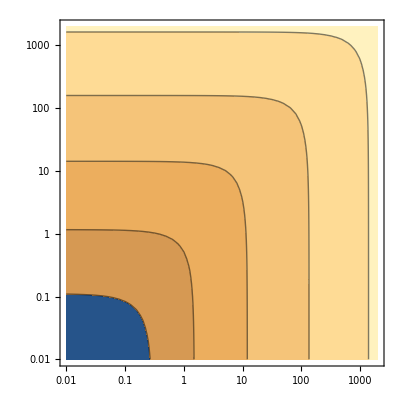

```mathematica
(* Open, kappa < 0, 2 real roots: gm(x) > 2 kt^3/mt^2 *)

Pp[rt_,mt_,kt_]:=-4/3 rt-kt^2;
Qq[rt_,mt_,kt_]:=-mt^2/2+kt^3-4 kt rt;
xh[rt_,mt_,kt_]:=(-Qq[rt,mt,kt]+√(Qq[rt,mt,kt]^2+Pp[rt,mt,kt]^3))^(1/3);
z0[rt_,mt_,kt_]:=2 kt+xh[rt,mt,kt]-Pp[rt,mt,kt]/xh[rt,mt,kt];
e0[rt_,mt_,kt_]:=z0[rt,mt,kt]^(1/2);
app[rt_,mt_,kt_]:=1/2((+e0[rt,mt,kt])+√(-(+e0[rt,mt,kt])^2-2mt/(+e0[rt,mt,kt])+6 kt));
apm[rt_,mt_,kt_]:=1/2((-e0[rt,mt,kt])+√(-(-e0[rt,mt,kt])^2-2mt/(-e0[rt,mt,kt])+6 kt));
amp[rt_,mt_,kt_]:=1/2((+e0[rt,mt,kt])-√(-(+e0[rt,mt,kt])^2-2mt/(+e0[rt,mt,kt])+6 kt));
amm[rt_,mt_,kt_]:=1/2((-e0[rt,mt,kt])-√(-(-e0[rt,mt,kt])^2-2mt/(-e0[rt,mt,kt])+6 kt));
zerocheck[rt_,mt_,kt_]:=app[rt,mt,kt]+apm[rt,mt,kt]+amp[rt,mt,kt]+amm[rt,mt,kt]

a1[rt_,mt_,kt_]:=apm[rt,mt,kt];
a2[rt_,mt_,kt_]:=app[rt,mt,kt];
a3[rt_,mt_,kt_]:=amp[rt,mt,kt];
a4[rt_,mt_,kt_]:=amm[rt,mt,kt];
mm[rt_,mt_,kt_]:=((a2[rt,mt,kt]-a3[rt,mt,kt])(a1[rt,mt,kt]-a4[rt,mt,kt]))/((a1[rt,mt,kt]-a3[rt,mt,kt])(a2[rt,mt,kt]-a4[rt,mt,kt]));

a1p[rt_,mt_,kt_]:=a2[rt,mt,kt];
a2p[rt_,mt_,kt_]:=a3[rt,mt,kt];
a3p[rt_,mt_,kt_]:=a1[rt,mt,kt];
a4p[rt_,mt_,kt_]:=a4[rt,mt,kt];

a12[rt_,mt_,kt_]:=a1p[rt,mt,kt]-a2p[rt,mt,kt];
a13[rt_,mt_,kt_]:=a1p[rt,mt,kt]-a3p[rt,mt,kt];
a14[rt_,mt_,kt_]:=a1p[rt,mt,kt]-a4p[rt,mt,kt];
a23[rt_,mt_,kt_]:=a2p[rt,mt,kt]-a3p[rt,mt,kt];
a24[rt_,mt_,kt_]:=a2p[rt,mt,kt]-a4p[rt,mt,kt];
a34[rt_,mt_,kt_]:=a3p[rt,mt,kt]-a4p[rt,mt,kt];
m0[rt_,mt_,kt_]:=(a12[rt,mt,kt] a34[rt,mt,kt])/(a13[rt,mt,kt] a24[rt,mt,kt]);
CK[rt_,mt_,kt_]:=a13[rt,mt,kt](a34[rt,mt,kt]^2-a12[rt,mt,kt]^2-4/3 a14[rt,mt,kt] a24[rt,mt,kt]);
CE[rt_,mt_,kt_]:=8 kt*(a13[rt,mt,kt] a24[rt,mt,kt])/a23[rt,mt,kt];
CPi[rt_,mt_,kt_]:=(a13[rt,mt,kt]^2-a24[rt,mt,kt]^2)(a14[rt,mt,kt]-a23[rt,mt,kt]);
Sanalytic[rt_,mt_,kt_]:=(√3)/24*a23[rt,mt,kt]/(√(a13[rt,mt,kt] a24[rt,mt,kt]))(CK[rt,mt,kt]*EllipticK[m0[rt,mt,kt]]+CE[rt,mt,kt] EllipticE[m0[rt,mt,kt]]+CPi[rt,mt,kt] EllipticPi[a12[rt,mt,kt]/a13[rt,mt,kt],m0[rt,mt,kt]])
(*Table2=Table[{10^RT,10^MT,Abs[Sanalytic[10^((4/3)RT),10^MT,-1]]},{RT,-2,3.3,1/10.},{MT,-2,3.3,1/10.}]*)
Plot2a=ListPlot3D[Flatten[Table2,1],ScalingFunctions->{"Log","Log","Log"},PlotRange->{10^-2,10^3.4},Mesh->{{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]},{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]}}]
Plot2b=ListContourPlot[Flatten[Table2,1],PlotRange->{{10^-2,10^3.3},{10^-2,10^3.3},{10^-6,10^3.4}},Contours->{Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]},ScalingFunctions->{"Log","Log","Log"},ContourShading->colorlist1]
```

```mathematica
Pst[rt_,mt_]:=+4/3 rt
Qst[rt_,mt_]:=-1/8 mt^2
xst[rt_,mt_]:=(-Qst[rt,mt]+√(Qst[rt,mt]^2+Pst[rt,mt]^3))^(1/3)
est[rt_,mt_]:=Re[(xst[rt,mt]-Pst[rt,mt]/xst[rt,mt])^(1/2)]
ast[rt_,mt_]:=1/2*(est[rt,mt]+√(-est[rt,mt]^2+mt/est[rt,mt]))
Omegakst[rt_,mt_,kt_]:=-3 kt*ast[rt,mt]^2*((rt+mt*ast[rt,mt]-3 kt ast[rt,mt]^2+ast[rt,mt]^4)^-1)

Table3=Table[{10^RT,10^MT,Abs[-Omegakst[10^((4/3)RT),10^MT,+1]]},{RT,-2,3.4,1/30.},{MT,-2,3.4,1/30.}]
Plot3a=ListPlot3D[Flatten[Table3,1],ScalingFunctions->{"Log","Log","Log"},PlotRange->{10^-2.3,10^2},Mesh->{{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]},{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]}}]
Plot3b=ListContourPlot[Flatten[Table3,1],PlotRange->{{10^-2,10^3.4},{10^-2,10^3.4},{10^-6,10^4}},Contours->{Log[10^-2],Log[10^-1.5],Log[10^-1],Log[10^-0.5],Log[10^0],Log[10^0.5],Log[10^1]},ScalingFunctions->{"Log","Log","Log"}]
colorlist2=Cases[Plot3b[[1]],{___,clr_RGBColor,_GraphicsGroup}:>clr,All];

Table4=Table[{10^RT,10^MT,Abs[-Omegakst[10^((4/3)RT),10^MT,-1]]},{RT,-2,3.4,1/30.},{MT,-2,3.4,1/30.}]
Plot4a=ListPlot3D[Flatten[Table4,1],ScalingFunctions->{"Log","Log","Log"},PlotRange->{10^-2.3,10^2},Mesh->{{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]},{Log[10^-2],Log[10^-1],Log[10^0],Log[10^1],Log[10^2],Log[10^3]}}]
Plot4b=ListContourPlot[Flatten[Table4,1],PlotRange->{{10^-2,10^3.4},{10^-2,10^3.4},{10^-6,10^4}},Contours->{Log[10^-2],Log[10^-1.5],Log[10^-1],Log[10^-0.5],Log[10^0],Log[10^0.5],Log[10^1]},ScalingFunctions->{"Log","Log","Log"},ContourShading->colorlist2]
```

{{{0.01,0.01,1.04773},{0.01,0.0107978,1.04894},{0.01,0.0116591,1.05024},{0.01,0.0125893,1.05163},156,{0.01,2154.43,0.00960765},{0.01,2326.31,0.00912403},{0.01,2511.89,0.00866497}},161,{1}}
 |  |  |  |

-Graphics3D-

-Graphics-

{{{0.01,0.01,0.956429},{0.01,0.0107978,0.955423},{0.01,0.0116591,0.954349},{0.01,0.0125893,0.953201},156,{0.01,2154.43,0.00942651},{0.01,2326.31,0.00896052},{0.01,2511.89,0.00851736}},161,{1}}
 |  |  |  |

-Graphics3D-

-Graphics-